Wolfram Online Mini Campus. Part 5

Instagram Posts
Pinterest Posts
"Translation" of SageMath Online Mini Campus. Part 5

Functions as Art Objects
Colorized Curves

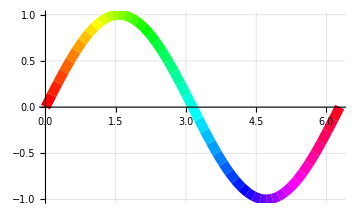

```mathematica
Show[Table[Plot[Sin[x],{x,i*Pi/24,(i+1)*Pi/24},PlotStyle->{Hue[i/48],Thickness[0.02]}],{i,Range[0,47,1]}],
         ImageSize->Medium,GridLines->Automatic,PlotRange->All]
```

Mesh Surfaces

```mathematica
k=7; f1[x_,y_,z_]=x^2/9+y^2/16-z^2/25; f2[x_,y_,z_]=x^2/4+y^2/9-z^2/16;
cp1=ContourPlot3D[f1[x,y,z]==1,{x,-k,k},{y,-k,k},{z,-k,k},Mesh->20,MeshStyle->Blue,ContourStyle->{Blue,Opacity[0.1]}];
cp2=ContourPlot3D[f2[x,y,z]==0,{x,-k,k},{y,-k,k},{z,-k,k},Mesh->30,MeshStyle->Red,ContourStyle->{Red,Opacity[0.2]}];
Show[cp1,cp2,Boxed->False,Axes->False]
```

-Graphics3D-

Plotting with Parameters

```mathematica
Manipulate[Show[Table[Plot[Sin[t-2*l]-t^2,{t,-1,1},PlotStyle->Hue[Sin[l/L]]],{l,Range[-1.25,1.25,0.05]}],
                                 PlotRange->All,Axes->False],{L,Range[1,10,1]}]
```

Limits & Plotting

```mathematica
F[x_,y_]=(1-Sqrt[1-x^2+x*y^3-y^4])/Sin[x^2+y^4]; FL[x_,y_]=Limit[F[x,y],{x,y}->{0,0}];
Plot3D[{F[x,y],FL[x,y]},{x,-1/4,1/4},{y,-1/4,1/4},PlotRange->All,PlotStyle->{Opacity[0.9],Opacity[0.4]},
               Mesh->False,PlotTheme->"VibrantColor",Boxed->False,Axes->False]
```

-Graphics3D-

Integration & Plotting

```mathematica
G[x_]=Integrate[Cos[x^2]*Exp[x],x,GeneratedParameters -> C];
Plot[Evaluate[{G[x]/.Table[{C[1]->i},{i,Range[0,10,5]}]}],{x,3,5},PlotTheme->"Detailed"]
```

-Graphics-

Logical Functions

```mathematica
bc=Tuples[{False,True},10]; Length[bc]
LF=Function[{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10},
                             ((x1||(! x2))&&(x3||(!x4)))&&((x3||(!x4))&&(x5||(!x6)))&&((x5||(!x6))&&(x7||(!x8)))&&((x7||(! x8))&&(x9||(! x10)))];
LFvalues=Table[Apply[lf,bc[[i]]],{i,Range[1,Length[bc],1]}]; Count[LFvalues,True]
```

1024

243

Artificial Clusters

```mathematica
makeCluster[class_,μ_,ρ_]:=RandomVariate[MultinormalDistribution[μ,{{1,4ρ}, {4 ρ,4}}],500] -> class;
clusters=makeCluster@@@{{1,{1.5,1.8},-.2},{2,{-1.5,1.1},.3},{3,{-1.6,-2.3},-.4},{4,{1.8,-2.2},.1}};
lp1=ListPlot[Keys[clusters],PlotStyle ->"BrightBands"];
```

```mathematica
clf=Classify[Flatten[Thread/@clusters],Method->"NearestNeighbors"]
```

ClassifierFunction[…]

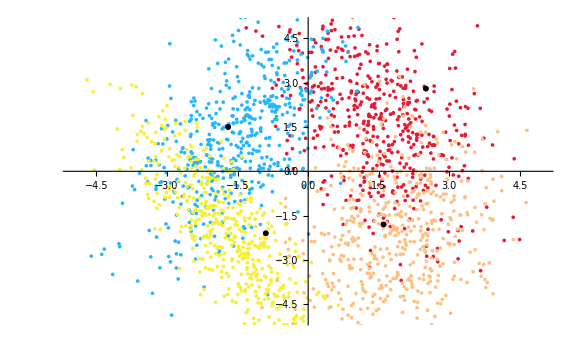

```mathematica
sample={{2.5,2.8},{-1.7,1.5},{-0.9,-2.1},{1.6,-1.8}};
lp2=ListPlot[List/@sample,PlotMarkers->clf[sample],PlotStyle->Black];
Show[lp1,lp2,ImageSize->Large,PlotRange->{{-5,5},{-5,5}}]
```

HTML Objects

```mathematica
EmbeddedHTML["<ul style='list-style-type:circle;'>
<li style='color:#3636ff;'>Coffee</li><li style='color:#36ff36;'>Tea</li><li style='color:#ff3636;'>Milk</li>
</ul>"]
```

Null«156»<ul style='list-style-type:circle;'>
<li style='color:#3636ff;'>Coffee</li><li style='color:#36ff36;'>Tea</li><li style='color:#ff3636;'>Milk</li>
</ul>

```mathematica
EmbeddedHTML["<svg width='150' height='150'>
<circle style='fill:steelblue; stroke:silver;' stroke-width='5' cx='75' cy='75' r='50'/>
</svg>"]
```

Null<svg width='150' height='150'>
<circ…h='5' cx='75' cy='75' r='50'/>
</svg><svg width='150' height='150'>
<circle style='fill:steelblue; stroke:silver;' stroke-width='5' cx='75' cy='75' r='50'/>
</svg>